```mathematica
Keys[allGraphs2]
```

{0,1,2}

```mathematica
Keys[allGraphs2[0]]
```

{signature,matrix,graph,vertexsets,vertices,edges,relations,links,parents,children,comp,compwhy,colofour,colortable,colofournull,colofourrealnull}

```mathematica
ShowGraph2Least[k_,prop_:"comp"]:=Labeled[Tooltip[ShowGraph[allGraphs2,k],allGraphs2[k,prop <>"why"]],Style[allGraphs2[k,prop],Blue],Top]
```

```mathematica
Table[Labeled[ShowGraph2Least[k],allGraphs2[k,"colofour"]],{k,0,2}]
```

{-Graphics-0Greaterv12+v1x2,-Graphics-1Greaterv1x2,-Graphics-2Greaterv12}

```mathematica
Keys[allGraphs3[0]]
```

{signature,matrix,graph,vertexsets,vertices,edges,relations,links,parents,children,comp,compwhy,colofour,colortable,colofournull,colofourrealnull}

```mathematica
ShowGraph3Least[k_]:=Framed[ShowGraph[allGraphs3,k]]
```

```mathematica
Table[Labeled[ShowGraph3Least[k],allGraphs3[k,"colofour"]],{k,Keys[allGraphs3]}]
```

{-Graphics-0Greaterv123+v12x3+v13x2+v1x23+v1x2x3,-Graphics-9Greaterv13x2+v1x23+v1x2x3,-Graphics-12Greaterv1x23+v1x2x3,-Graphics-13Greaterv1x2x3,-Graphics-14Greaterv1x23,-Graphics-16Greaterv13x2,-Graphics-10Greaterv13x2+v1x2x3,-Graphics-18Greaterv123+v12x3,-Graphics-22Greaterv12x3,-Graphics-26Greaterv123,-Graphics-3Greaterv12x3+v1x23+v1x2x3,-Graphics-4Greaterv12x3+v1x2x3,-Graphics-6Greaterv123+v13x2,-Graphics-1Greaterv12x3+v13x2+v1x2x3,-Graphics-2Greaterv123+v1x23}

```mathematica
Table[ShowGraph[allGraphs4,k],{k,Keys[allGraphs4]}]
```

{-Graphics-0,-Graphics-243,-Graphics-324,-Graphics-351,-Graphics-360,-Graphics-363,-Graphics-364,-Graphics-365,-Graphics-367,-Graphics-361,-Graphics-369,-Graphics-373,-Graphics-377,-Graphics-354,-Graphics-355,-Graphics-357,-Graphics-352,-Graphics-353,-Graphics-382,-Graphics-391,-Graphics-400,-Graphics-333,-Graphics-336,-Graphics-337,-Graphics-334,-Graphics-342,-Graphics-346,-Graphics-327,-Graphics-328,-Graphics-325,-Graphics-414,-Graphics-442,-Graphics-445,-Graphics-448,-Graphics-473,-Graphics-417,-Graphics-270,-Graphics-279,-Graphics-282,-Graphics-283,-Graphics-286,-Graphics-280,-Graphics-273,-Graphics-274,-Graphics-276,-Graphics-271,-Graphics-300,-Graphics-309,-Graphics-252,-Graphics-255,-Graphics-256,-Graphics-257,-Graphics-253,-Graphics-246,-Graphics-247,-Graphics-244,-Graphics-245,-Graphics-486,-Graphics-576,-Graphics-606,-Graphics-607,-Graphics-608,-Graphics-637,-Graphics-577,-Graphics-666,-Graphics-697,-Graphics-728,-Graphics-516,-Graphics-517,-Graphics-546,-Graphics-487,-Graphics-488,-Graphics-81,-Graphics-108,-Graphics-117,-Graphics-120,-Graphics-121,-Graphics-122,-Graphics-118,-Graphics-111,-Graphics-112,-Graphics-109,-Graphics-110,-Graphics-136,-Graphics-145,-Graphics-90,-Graphics-93,-Graphics-94,-Graphics-97,-Graphics-91,-Graphics-84,-Graphics-85,-Graphics-87,-Graphics-82,-Graphics-162,-Graphics-190,-Graphics-193,-Graphics-218,-Graphics-165,-Graphics-168,-Graphics-27,-Graphics-36,-Graphics-39,-Graphics-40,-Graphics-37,-Graphics-45,-Graphics-49,-Graphics-30,-Graphics-31,-Graphics-28,-Graphics-54,-Graphics-63,-Graphics-72,-Graphics-9,-Graphics-12,-Graphics-13,-Graphics-14,-Graphics-16,-Graphics-10,-Graphics-18,-Graphics-22,-Graphics-26,-Graphics-3,-Graphics-4,-Graphics-6,-Graphics-1,-Graphics-2}

```mathematica
allGraphs3AtomKeys
```

{13,14,16,22,26}

```mathematica
AllBut[all_,buts_]:=Select[all,!MemberQ[buts,#]&]
```

```mathematica
FullPoset[all_]:=Block[{result={}, vertices={},edges={}, intermediate, added={}},
Table[
Table[
Table[
If[all[main,"colofour"]==all[first,"colofour"]+all[second,"colofour"],
AppendTo[result,{main,{first,second}}]
]
,
{second,AllBut[Keys[all],{main, first}]}
],
{first,AllBut[Keys[all],{main}]}
]
,{main,Keys[all]}
];
vertices = Keys[all];
Table[
intermediate=Sort[{res[[1]],res[[2,1]],res[[2,2]]}];
AppendTo[edges,res[[1]]->intermediate];
AppendTo[edges,intermediate->res[[2,1]]];
AppendTo[edges,intermediate->res[[2,2]]];
AppendTo[added,intermediate]
,{res,result}];
edges=DeleteDuplicates[edges];
added=DeleteDuplicates[added];
vertices=Join[added,vertices];
Graph[
vertices,
edges,
VertexLabels->Join[
Map[#->Labeled[Framed[ShowGraph[all,#]],Style[Factor[ChromaticPolynomial[all[#,"graph"],4]],Green]]&,Keys[all]],
Map[#->Tooltip["*",Column[#]]&,added]
],
VertexStyle->Map[#->Blue&,added],
GraphLayout->"LayeredDigraphEmbedding"
]
];
```

```mathematica
Subgraph
```

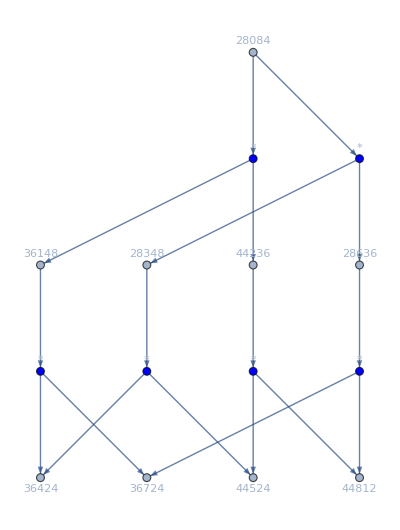

```mathematica
With[{g=FullPoset[allGraphs4]},
Graph[Subgraph[g,VertexOutComponent[g,280]],ImageSize->400]
]
```

```mathematica
VertexOutComponent[FullPoset[allGraphs4],280]
```

{280,13834872787,6354345419,361,442,283,286,15072933341,30907044677,14402239919,14856649111,364,367,445,448}

```mathematica
With[{g=FullPoset[allGraphs5]},
Graph[Subgraph[g,VertexOutComponent[g,lambdaKey]],ImageSize->400]
]
```

$Aborted

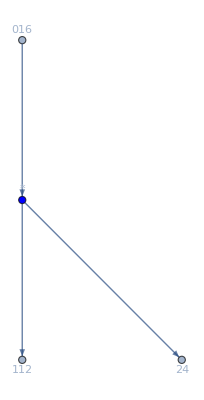

```mathematica
FullPoset[allGraphs2]
```

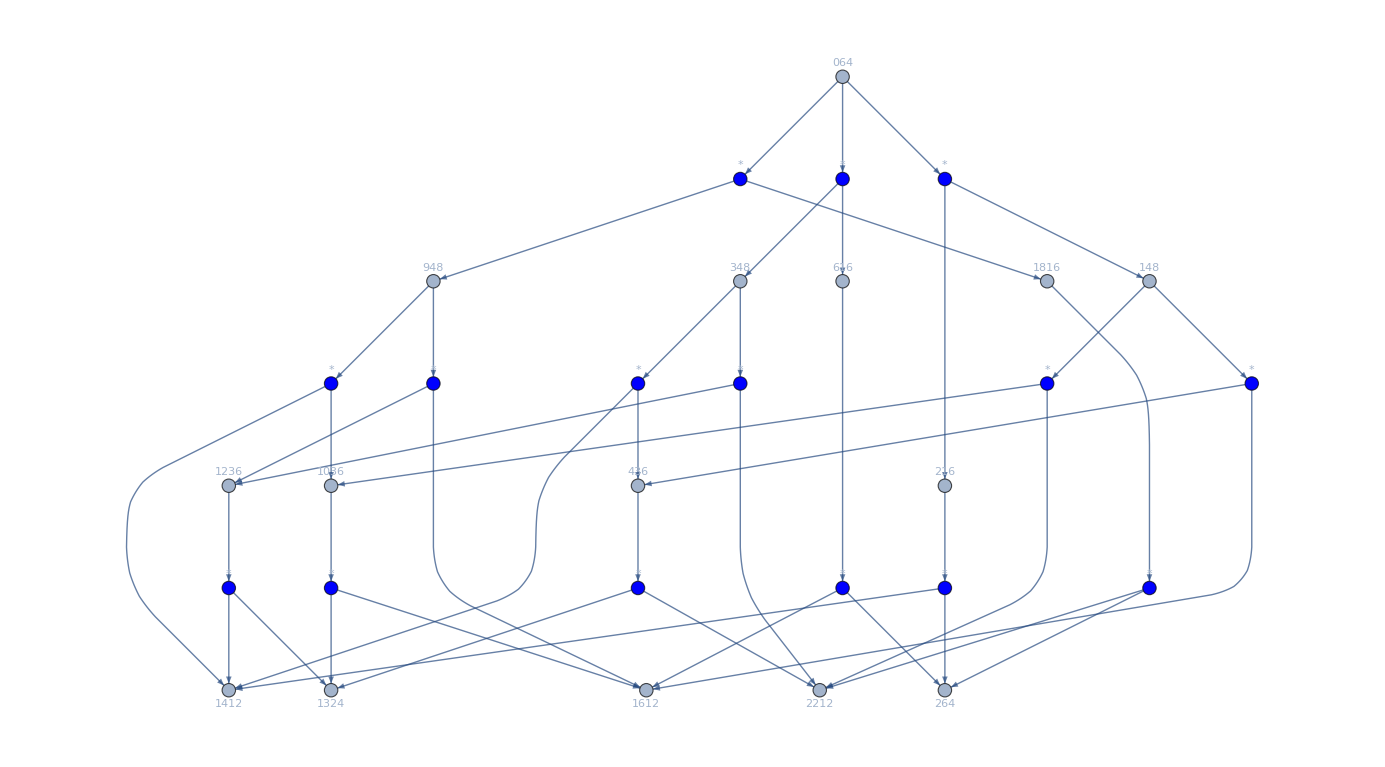

```mathematica
FullPoset[allGraphs3]
```

```mathematica
Keys[allGraphs4[0]]
```

{signature,matrix,graph,vertexsets,vertices,edges,relations,links,parents,children,comp,compwhy,colofour,colortable,colofournull,colofourrealnull}

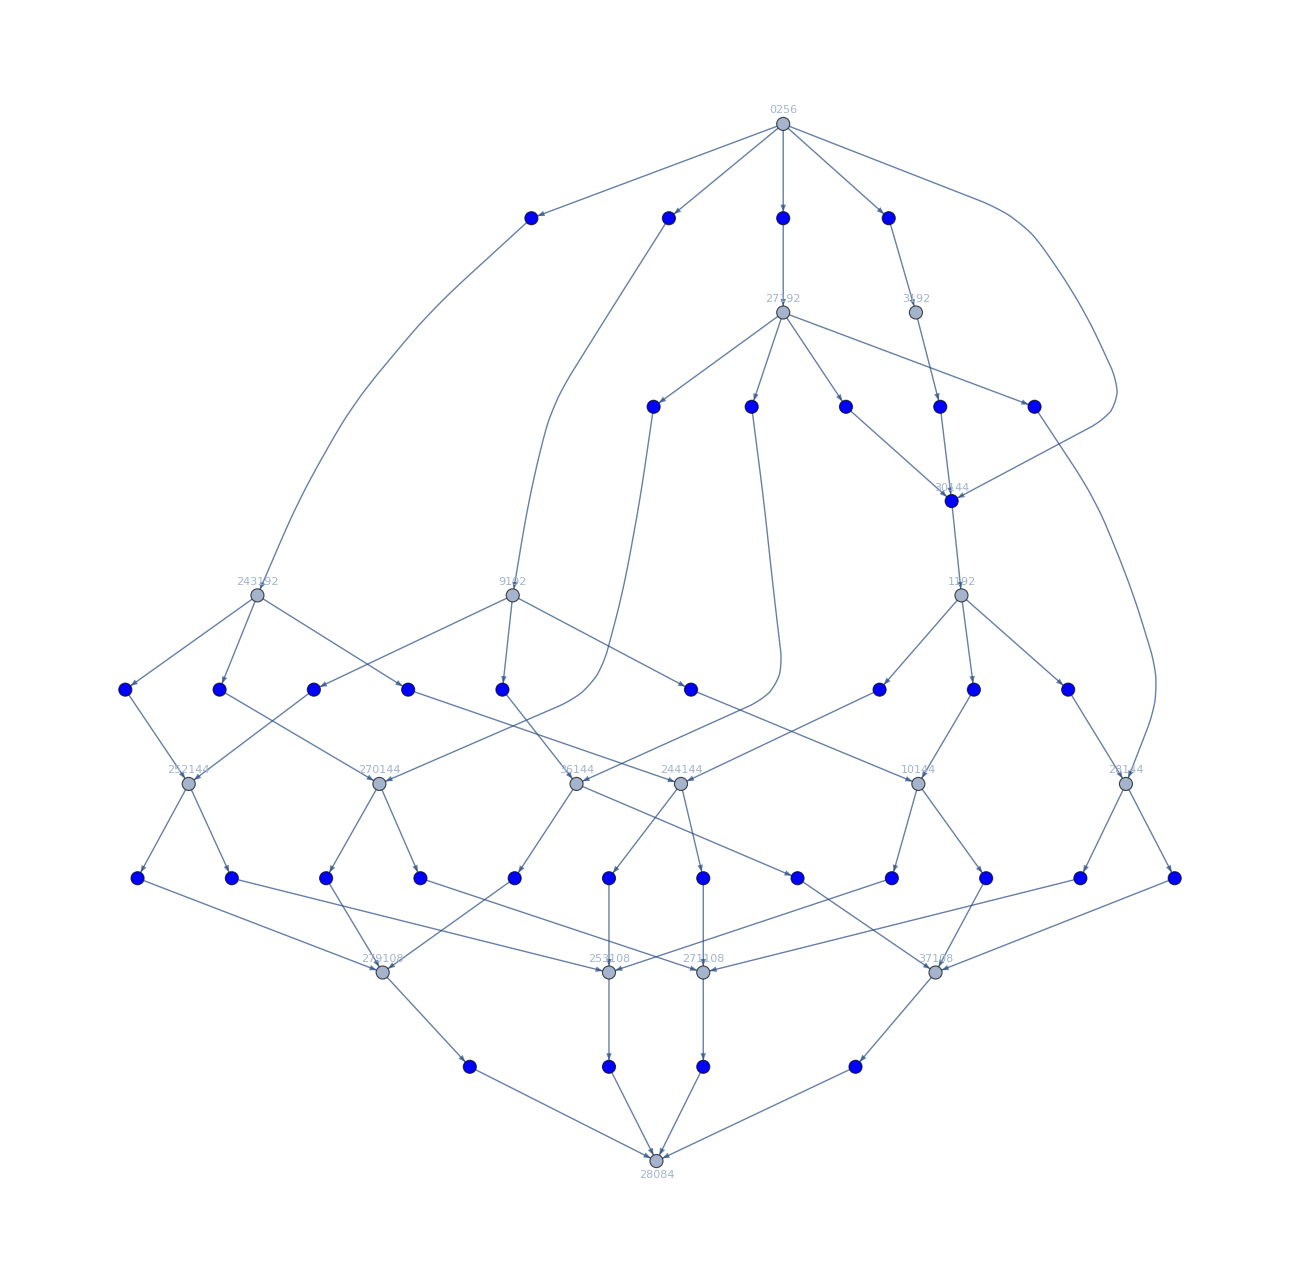

```mathematica
With[{g=FullPoset[allGraphs4]},
Graph[Subgraph[g,VertexInComponent[g,280]],ImageSize->400]
]
```

```mathematica
pos4=FullPoset[allGraphs4]
```

```mathematica
FullPosetNull[all_]:=Block[{result={}, vertices={},edges={}, intermediate, added={}},
Table[
Table[
Table[
If[all[main,"colofourrealnull"]==all[first,"colofourrealnull"]+all[second,"colofourrealnull"],
AppendTo[result,{main,{first,second}}]
]
,
{second,AllBut[Keys[all],{main, first}]}
],
{first,AllBut[Keys[all],{main}]}
]
,{main,Keys[all]}
];
vertices = Keys[all];
Table[
intermediate=Sort[{res[[1]],res[[2,1]],res[[2,2]]}];
AppendTo[edges,res[[1]]->intermediate];
AppendTo[edges,intermediate->res[[2,1]]];
AppendTo[edges,intermediate->res[[2,2]]];
AppendTo[added,intermediate]
,{res,result}];
edges=DeleteDuplicates[edges];
added=DeleteDuplicates[added];
vertices=Join[added,vertices];
Graph[
vertices,
edges,
VertexLabels->Join[
Map[#->Labeled[Framed[ShowGraph[all,#]],Style[Factor[ChromaticPolynomial[all[#,"graph"],4]],Green]]&,Keys[all]],
Map[#->Tooltip["*",Column[#]]&,added]
],
VertexStyle->Map[#->Blue&,added],
GraphLayout->"LayeredDigraphEmbedding"
]
]
```

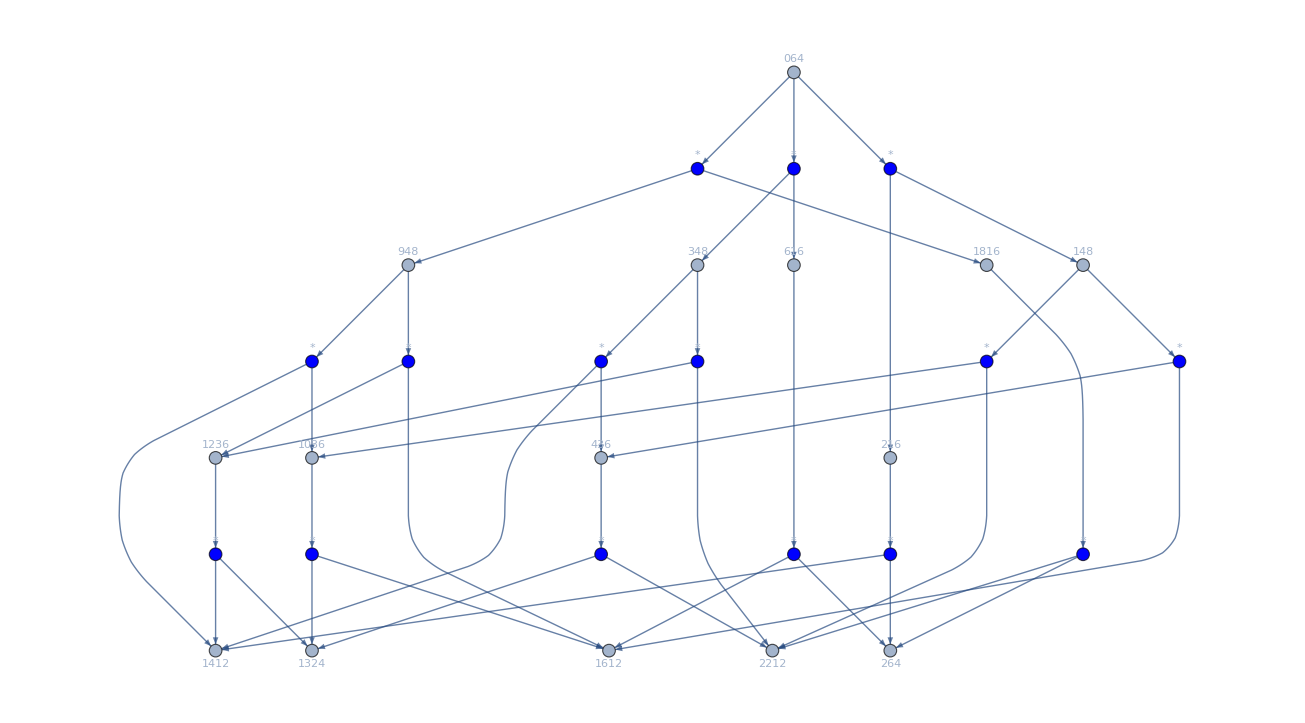

```mathematica
FullPosetNull[allGraphs3]
```